```mathematica
Parametrization of GPDs used in GK model for pi0 production
```

```mathematica
\tilde{H}
```

NIntegrate::nlim: y = 1.11111 (-0.1+x) HeavisideTheta[-0.1+x] is not a valid limit of integration.

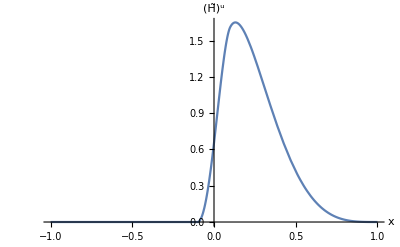

NIntegrate::nlim: y = 1.11111 (-0.1+x) HeavisideTheta[-0.1+x] is not a valid limit of integration.

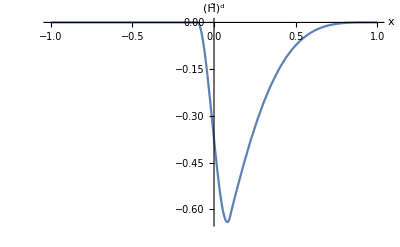

```mathematica
cu=List[cu=0.213,0.929,12.59,-12.57,0.0];
cd=List[cd=-0.204,-0.940,-0.314,1.524,0.0];
pu[y_]:=y^(-0.32)*(1-y)^0*(0.213+0.929*Sqrt[y]+12.59*y-12.57*y^(3/2)+0.0*y^2);
pd[y_]:=y^(-0.32)*(1-y)^0*(-0.204-0.940*Sqrt[y]-0.314*y+1.524*y^(3/2)+0.0*y^2);
fu[y_]:=(-0.961*Log[y]+0.545)*(1-y)^3+(1.264)*y*(1-y)^2;
fd[y_]:=(-0.861*Log[y]+0.206)*(1-y)^3+(4.198)*y*(1-y)^2;

lowery[x_,xi_]:=HeavisideTheta[x-xi]*(x-xi)/(1-xi);
uppery[x_,xi_]:=HeavisideTheta[x+xi]*(x+xi)/(1+xi);

Htildeu[x_,xi_,t_]:=3/(4*xi^3)*NIntegrate[pu[y]*Exp[t*fu[y]]*(xi^2*(1-y)^2-(x-y)^2),{y,lowery[x,xi],uppery[x,xi]}];
Htilded[x_,xi_,t_]:=3/(4*xi^3)*NIntegrate[pd[y]*Exp[t*fd[y]]*(xi^2*(1-y)^2-(x-y)^2),{y,lowery[x,xi],uppery[x,xi]}];

Plot[Htildeu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^u"}]

Plot[Htilded[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(H̃)^d"}]
```

## \tilde{E}

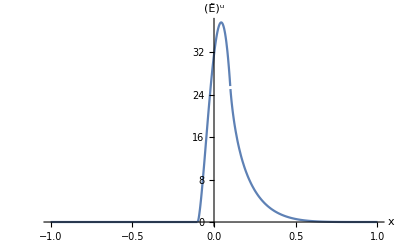

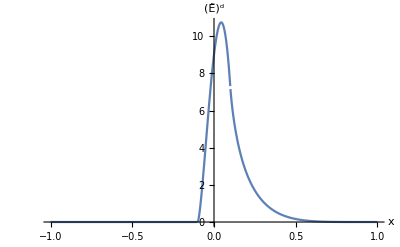

```mathematica
Clear[k];

EtildeAlpha0=0.48;
EtildeAlphaprime=0.45;
Etildeb=0.9;
EtildeNu=14;
EtildeNd=4;

k[t_]=EtildeAlpha0+EtildeAlphaprime*t;

(*When x+xi < 0.0*)
D1=0.0;
(*When x-xi < 0.0*)
D2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-k[t])*(xi^2-x+(2+i-k[t])*xi*(1-x))/((1+i-k[t])*(2+i-k[t])*(3+i-k[t]));
(*Else*)
D3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-k[t])*(2+i-k[t])*(3+i-k[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-k[t])-((x-xi)/(1-xi))^(2+i-k[t]))+xi*(1-x)*(2+i-k[t])*(((x+xi)/(1+xi))^(2+i-k[t])+((x-xi)/(1-xi))^(2+i-k[t])));

DD[i_,x_,xi_,t_]= If[x<-xi,D1,If[-xi≤x≤xi,D2[i,x,xi,t],D3[i,x,xi,t]]];

Etildeu[x_,xi_,t_]:=Exp[Etildeb*t]*(EtildeNu*DD[0,x,xi,t]-2*EtildeNu*DD[1,x,xi,t]+EtildeNu*DD[2,x,xi,t]);
Etilded[x_,xi_,t_]:=Exp[Etildeb*t]*(EtildeNd*DD[0,x,xi,t]-2*EtildeNd*DD[1,x,xi,t]+EtildeNd*DD[2,x,xi,t]);

Plot[Etildeu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^u"}]

Plot[Etilded[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ẽ)^d"}]
```

## H_T

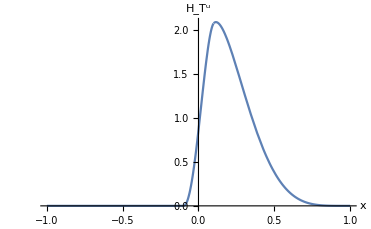

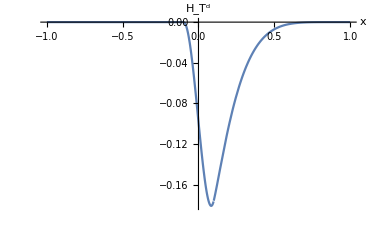

```mathematica
UpHTAlpha0=-0.17;
UpHTAlphaprime=0.45;
UpHTb=0.3;

DownHTAlpha0=-0.17;
DownHTAlphaprime=0.45;
DownHTb=0.3;

HTNu=1.1;
HTNd=-0.3;

UpHTk[t_]=UpHTAlpha0+UpHTAlphaprime*t;
DownHTk[t_]=DownHTAlpha0+DownHTAlphaprime*t;

(*When x+xi < 0.0*)
UpHTD1=0.0;
(*When x-xi < 0.0*)
UpHTD2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-UpHTk[t])*(xi^2-x+(2+i-UpHTk[t])*xi*(1-x))/((1+i-UpHTk[t])*(2+i-UpHTk[t])*(3+i-UpHTk[t]));
(*Else*)
UpHTD3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-UpHTk[t])*(2+i-UpHTk[t])*(3+i-UpHTk[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-UpHTk[t])-((x-xi)/(1-xi))^(2+i-UpHTk[t]))+xi*(1-x)*(2+i-UpHTk[t])*(((x+xi)/(1+xi))^(2+i-UpHTk[t])+((x-xi)/(1-xi))^(2+i-UpHTk[t])));

(*UpHTDD[i_,x_,xi_,t_]= If[x<-xi,UpHTD1,If[-xi≤x≤xi,UpHTD2[i,x,xi,t],UpHTD3[i,x,xi,t]]];*)

UpHTDD[i_,x_,xi_,t_]=If[Abs[xi]>0.001, If[x<-xi,UpHTD1,If[-xi≤x≤xi,UpHTD2[i,x,xi,t],UpHTD3[i,x,xi,t]]],If[x>0.0,If[(i-UpHTk[t])>0.0,(1-x)^3*(x)^(i-UpHTk[t]),0.0],0.0]];

(*When x+xi < 0.0*)
DownHTD1=0.0;
(*When x-xi < 0.0*)
DownHTD2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-DownHTk[t])*(xi^2-x+(2+i-DownHTk[t])*xi*(1-x))/((1+i-DownHTk[t])*(2+i-DownHTk[t])*(3+i-DownHTk[t]));
(*Else*)
DownHTD3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-DownHTk[t])*(2+i-DownHTk[t])*(3+i-DownHTk[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-DownHTk[t])-((x-xi)/(1-xi))^(2+i-DownHTk[t]))+xi*(1-x)*(2+i-DownHTk[t])*(((x+xi)/(1+xi))^(2+i-DownHTk[t])+((x-xi)/(1-xi))^(2+i-DownHTk[t])));

(*DownHTDD[i_,x_,xi_,t_]= If[x<-xi,DownHTD1,If[-xi≤x≤xi,DownHTD2[i,x,xi,t],DownHTD3[i,x,xi,t]]];*)

DownHTDD[i_,x_,xi_,t_]=If[Abs[xi]>0.001, If[x<-xi,DownHTD1,If[-xi≤x≤xi,DownHTD2[i,x,xi,t],DownHTD3[i,x,xi,t]]],If[x>0.0,If[(i-DownHTk[t])>0.0,(1-x)^3*(x)^(i-DownHTk[t]),0.0],0.0]];

HTu[x_,xi_,t_]:=HTNu*Exp[UpHTb*t]*(3.653*UpHTDD[0,x,xi,t]-0.583*UpHTDD[0.5,x,xi,t]+19.807*UpHTDD[1,x,xi,t]-23.487*UpHTDD[1.5,x,xi,t]-23.46*UpHTDD[2,x,xi,t]+24.07*UpHTDD[2.5,x,xi,t]);
HTd[x_,xi_,t_]:=HTNd*Exp[DownHTb*t]*(1.924*DownHTDD[0,x,xi,t]+0.179*DownHTDD[0.5,x,xi,t]-7.775*DownHTDD[1,x,xi,t]+3.504*DownHTDD[1.5,x,xi,t]+5.851*DownHTDD[2,x,xi,t]-3.683*DownHTDD[2.5,x,xi,t]);

Plot[HTu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","H_T^u"}]

Plot[HTd[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","H_T^d"}]
```

## \bar{E}_T

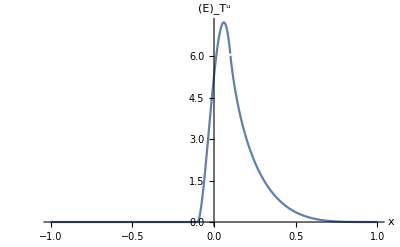

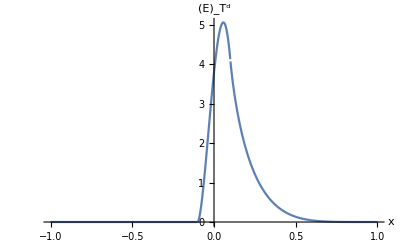

```mathematica
UpEbarTAlpha0=0.3;
UpEbarTAlphaprime=0.45;
UpEbarTb=0.5;

DownEbarTAlpha0=0.3;
DownEbarTAlphaprime=0.45;
DownEbarTb=0.5;

EbarTNu=4.83;
EbarTNd=3.57;

UpEbarTk[t_]=UpEbarTAlpha0+UpEbarTAlphaprime*t;
DownEbarTk[t_]=DownEbarTAlpha0+DownEbarTAlphaprime*t;

(*When x+xi < 0.0 for up quarks*)
UpEbarTD1=0.0;
(*When x-xi < 0.0*)
UpEbarTD2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-UpEbarTk[t])*(xi^2-x+(2+i-UpEbarTk[t])*xi*(1-x))/((1+i-UpEbarTk[t])*(2+i-UpEbarTk[t])*(3+i-UpEbarTk[t]));
(*Else*)
UpEbarTD3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-UpEbarTk[t])*(2+i-UpEbarTk[t])*(3+i-UpEbarTk[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-UpEbarTk[t])-((x-xi)/(1-xi))^(2+i-UpEbarTk[t]))+xi*(1-x)*(2+i-UpEbarTk[t])*(((x+xi)/(1+xi))^(2+i-UpEbarTk[t])+((x-xi)/(1-xi))^(2+i-UpEbarTk[t])));

(*UpEbarTDD[i_,x_,xi_,t_]= If[x<-xi,UpEbarTD1,If[-xi≤x≤xi,UpEbarTD2[i,x,xi,t],UpEbarTD3[i,x,xi,t]]];*)

UpEbarTDD[i_,x_,xi_,t_]=If[Abs[xi]>0.001, If[x<-xi,UpEbarTD1,If[-xi≤x≤xi,UpEbarTD2[i,x,xi,t],UpEbarTD3[i,x,xi,t]]],If[x>0.0,If[(i-UpEbarTk[t])>0.0,(1-x)^3*(x)^(i-UpEbarTk[t]),0.0],0.0]];


(*When x+xi < 0.0 for down quarks*)
DownEbarTD1=0.0;
(*When x-xi < 0.0*)
DownEbarTD2[i_,x_,xi_,t_]:=3/(2*xi^3)*((x+xi)/(1+xi))^(2+i-DownEbarTk[t])*(xi^2-x+(2+i-DownEbarTk[t])*xi*(1-x))/((1+i-DownEbarTk[t])*(2+i-DownEbarTk[t])*(3+i-DownEbarTk[t]));
(*Else*)
DownEbarTD3[i_,x_,xi_,t_]:=3/(2*xi^3)/((1+i-DownEbarTk[t])*(2+i-DownEbarTk[t])*(3+i-DownEbarTk[t]))*((xi^2-x)*(((x+xi)/(1+xi))^(2+i-DownEbarTk[t])-((x-xi)/(1-xi))^(2+i-DownEbarTk[t]))+xi*(1-x)*(2+i-DownEbarTk[t])*(((x+xi)/(1+xi))^(2+i-DownEbarTk[t])+((x-xi)/(1-xi))^(2+i-DownEbarTk[t])));

(*DownEbarTDD[i_,x_,xi_,t_]= If[x<-xi,DownEbarTD1,If[-xi≤x≤xi,DownEbarTD2[i,x,xi,t],DownEbarTD3[i,x,xi,t]]];*)

DownEbarTDD[i_,x_,xi_,t_]=If[Abs[xi]>0.001, If[x<-xi,DownEbarTD1,If[-xi≤x≤xi,DownEbarTD2[i,x,xi,t],DownEbarTD3[i,x,xi,t]]],If[x>0.0,If[(i-DownEbarTk[t])>0.0,(1-x)^3*(x)^(i-DownEbarTk[t]),0.0],0.0]];

EbarTu[x_,xi_,t_]:=EbarTNu*Exp[UpEbarTb*t]*(UpEbarTDD[0,x,xi,t]-UpEbarTDD[1,x,xi,t]);
EbarTd[x_,xi_,t_]:=EbarTNd*Exp[DownEbarTb*t]*(DownEbarTDD[0,x,xi,t]-2*DownEbarTDD[1,x,xi,t]+DownEbarTDD[2,x,xi,t]);

Plot[EbarTu[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ē)_T^u"}]

Plot[EbarTd[x,0.1,-0.1],{x,-1.0,1.0},PlotRange->All,AxesLabel->{"x","(Ē)_T^d"}]
```